# Kelvin Problem in 2-d plane strain

```mathematica
x = xo - xs
y = yo - ys
C0 = 1/ (4 * Pi *(1-ν))
r = Sqrt[x^2 + y^2]
g = -C0 * Log[r]
gx = -C0*x/r^2
gy = -C0*y/r^2
ux = fx/(2*μ)*((3-4*ν)*g - x*gx) + fy/(2*μ)*(-y*gx) 
uy = fx/(2*μ)*(-x*gy) + fy/(2*μ)*((3-4*ν)*g -y*gy)
```

xo-xs

yo-ys

1/(4 π (1-ν))

√((xo-xs)^2+(yo-ys)^2)

-Log[√((xo-xs)^2+(yo-ys)^2)]/(4 π (1-ν))

-(xo-xs)/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))

-(yo-ys)/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))

-(fy (xo-xs) (-yo+ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fx ((xo-xs)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

-(fx (-xo+xs) (yo-ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fy ((yo-ys)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

```mathematica
uxmod = ReplaceAll[ux,{ys->0,yo->1}]
uymod = ReplaceAll[uy,{ys->0,yo->1}]
uxint = Integrate[uxmod,{xs,-1,1}]
uyint = Integrate[uymod,{xs,-1,1}]
```

(fy (xo-xs))/(8 π (1+(xo-xs)^2) μ (1-ν))+(fx ((xo-xs)^2/(4 π (1+(xo-xs)^2) (1-ν))-((3-4 ν) Log[√(1+(xo-xs)^2)])/(4 π (1-ν))))/(2 μ)

-(fx (-xo+xs))/(8 π (1+(xo-xs)^2) μ (1-ν))+(fy (1/(4 π (1+(xo-xs)^2) (1-ν))-((3-4 ν) Log[√(1+(xo-xs)^2)])/(4 π (1-ν))))/(2 μ)

ConditionalExpression[-1/(16 π μ (-1+ν))(-16 fx (-1+ν)+8 fx (-1+ν) ArcTan[1-xo]+8 fx (-1+ν) ArcTan[1+xo]-(fy+fx (-1+xo) (-3+4 ν)) Log[2-2 xo+xo^2]+(fy+fx (1+xo) (-3+4 ν)) Log[2+2 xo+xo^2]), ]

ConditionalExpression[1/(16 π μ (-1+ν))(4 fy (-3+4 ν)+4 fy (1-2 ν) ArcTan[1-xo]+4 fy (1-2 ν) ArcTan[1+xo]+(fx+fy (-1+xo) (-3+4 ν)) Log[2+(-2+xo) xo]-(fx+fy (1+xo) (-3+4 ν)) Log[2+xo (2+xo)]), ]

```mathematica
Plot[ ReplaceAll[uxint,{fx -> 1, μ->1,ν->0.25}],{xo,-2,2}]
Plot[ ReplaceAll[uyint,{fy -> -1, μ->1,ν->0.25}],{xo,-2,2}]
```

-Graphics-

-Graphics-

```mathematica
(*uxint2 = Integrate[Integrate[uxmod2,{xo,-1,1}],yo]*)
uxint2 = Integrate[ux,xs,ys]
uxdefint2 = ReplaceAll[uxint2, {xs->1,ys->0.1}] + ReplaceAll[uxint2, {xs->-1,ys->-0.1}] - ReplaceAll[uxint2, {xs->1,ys->-0.1}] - ReplaceAll[uxint2, {xs->-1,ys->0.1}]
```

-1/(32 π μ (-1+ν))(-fy xo^2+2 fy xo xs-fy xs^2-6 fx xo yo-20 fx xs yo+6 fx xo ys+20 fx xs ys+8 fx xo yo ν+24 fx xs yo ν-8 fx xo ys ν-24 fx xs ys ν+2 fx (yo-ys)^2 (-7+8 ν) ArcTan[(xo-xs)/(yo-ys)]+2 fx (xo^2-2 xo xs+xs^2+(yo-ys)^2) (-3+4 ν) ArcTan[(yo-ys)/(xo-xs)]-6 fx xo yo Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]+6 fx xs yo Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]+fy yo^2 Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]+6 fx xo ys Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]-6 fx xs ys Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]-2 fy yo ys Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]+fy ys^2 Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]+8 fx xo yo ν Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]-8 fx xs yo ν Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]-8 fx xo ys ν Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]+8 fx xs ys ν Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]+fy xo^2 Log[√(-(xo-xs)^2)+yo-ys]+fx xo √(-(xo-xs)^2) Log[√(-(xo-xs)^2)+yo-ys]-2 fy xo xs Log[√(-(xo-xs)^2)+yo-ys]-fx √(-(xo-xs)^2) xs Log[√(-(xo-xs)^2)+yo-ys]+fy xs^2 Log[√(-(xo-xs)^2)+yo-ys]+fy xo^2 Log[√(-(xo-xs)^2)-yo+ys]-fx xo √(-(xo-xs)^2) Log[√(-(xo-xs)^2)-yo+ys]-2 fy xo xs Log[√(-(xo-xs)^2)-yo+ys]+fx √(-(xo-xs)^2) xs Log[√(-(xo-xs)^2)-yo+ys]+fy xs^2 Log[√(-(xo-xs)^2)-yo+ys])

-1/(32 π μ (-1+ν))(2. fx-fy+0.6 fx xo+2 fy xo-fy xo^2-20 fx yo-6 fx xo yo-2.4 fx ν-0.8 fx xo ν+24 fx yo ν+8 fx xo yo ν+2 fx (-0.1+yo)^2 (-7+8 ν) ArcTan[(-1+xo)/(-0.1+yo)]+2 fx (1-2 xo+xo^2+(-0.1+yo)^2) (-3+4 ν) ArcTan[(-0.1+yo)/(-1+xo)]-0.6 fx Log[1-2 xo+xo^2+(-0.1+yo)^2]+0.01 fy Log[1-2 xo+xo^2+(-0.1+yo)^2]+0.6 fx xo Log[1-2 xo+xo^2+(-0.1+yo)^2]+6 fx yo Log[1-2 xo+xo^2+(-0.1+yo)^2]-0.2 fy yo Log[1-2 xo+xo^2+(-0.1+yo)^2]-6 fx xo yo Log[1-2 xo+xo^2+(-0.1+yo)^2]+fy yo^2 Log[1-2 xo+xo^2+(-0.1+yo)^2]+0.8 fx ν Log[1-2 xo+xo^2+(-0.1+yo)^2]-0.8 fx xo ν Log[1-2 xo+xo^2+(-0.1+yo)^2]-8 fx yo ν Log[1-2 xo+xo^2+(-0.1+yo)^2]+8 fx xo yo ν Log[1-2 xo+xo^2+(-0.1+yo)^2]+fy Log[0.1+√(-(-1+xo)^2)-yo]+fx √(-(-1+xo)^2) Log[0.1+√(-(-1+xo)^2)-yo]-2 fy xo Log[0.1+√(-(-1+xo)^2)-yo]-fx √(-(-1+xo)^2) xo Log[0.1+√(-(-1+xo)^2)-yo]+fy xo^2 Log[0.1+√(-(-1+xo)^2)-yo]+fy Log[-0.1+√(-(-1+xo)^2)+yo]-fx √(-(-1+xo)^2) Log[-0.1+√(-(-1+xo)^2)+yo]-2 fy xo Log[-0.1+√(-(-1+xo)^2)+yo]+fx √(-(-1+xo)^2) xo Log[-0.1+√(-(-1+xo)^2)+yo]+fy xo^2 Log[-0.1+√(-(-1+xo)^2)+yo])+1/(32 π μ (-1+ν))(-2. fx-fy+0.6 fx xo-2 fy xo-fy xo^2+20 fx yo-6 fx xo yo+2.4 fx ν-0.8 fx xo ν-24 fx yo ν+8 fx xo yo ν+2 fx (-0.1+yo)^2 (-7+8 ν) ArcTan[(1+xo)/(-0.1+yo)]+2 fx (1+2 xo+xo^2+(-0.1+yo)^2) (-3+4 ν) ArcTan[(-0.1+yo)/(1+xo)]+0.6 fx Log[1+2 xo+xo^2+(-0.1+yo)^2]+0.01 fy Log[1+2 xo+xo^2+(-0.1+yo)^2]+0.6 fx xo Log[1+2 xo+xo^2+(-0.1+yo)^2]-6 fx yo Log[1+2 xo+xo^2+(-0.1+yo)^2]-0.2 fy yo Log[1+2 xo+xo^2+(-0.1+yo)^2]-6 fx xo yo Log[1+2 xo+xo^2+(-0.1+yo)^2]+fy yo^2 Log[1+2 xo+xo^2+(-0.1+yo)^2]-0.8 fx ν Log[1+2 xo+xo^2+(-0.1+yo)^2]-0.8 fx xo ν Log[1+2 xo+xo^2+(-0.1+yo)^2]+8 fx yo ν Log[1+2 xo+xo^2+(-0.1+yo)^2]+8 fx xo yo ν Log[1+2 xo+xo^2+(-0.1+yo)^2]+fy Log[0.1+√(-(1+xo)^2)-yo]+2 fy xo Log[0.1+√(-(1+xo)^2)-yo]+fy xo^2 Log[0.1+√(-(1+xo)^2)-yo]-fx √(-(1+xo)^2) Log[0.1+√(-(1+xo)^2)-yo]-fx xo √(-(1+xo)^2) Log[0.1+√(-(1+xo)^2)-yo]+fy Log[-0.1+√(-(1+xo)^2)+yo]+2 fy xo Log[-0.1+√(-(1+xo)^2)+yo]+fy xo^2 Log[-0.1+√(-(1+xo)^2)+yo]+fx √(-(1+xo)^2) Log[-0.1+√(-(1+xo)^2)+yo]+fx xo √(-(1+xo)^2) Log[-0.1+√(-(1+xo)^2)+yo])+1/(32 π μ (-1+ν))(-2. fx-fy-0.6 fx xo+2 fy xo-fy xo^2-20 fx yo-6 fx xo yo+2.4 fx ν+0.8 fx xo ν+24 fx yo ν+8 fx xo yo ν+2 fx (0.1+yo)^2 (-7+8 ν) ArcTan[(-1+xo)/(0.1+yo)]+2 fx (1-2 xo+xo^2+(0.1+yo)^2) (-3+4 ν) ArcTan[(0.1+yo)/(-1+xo)]+fy Log[-0.1+√(-(-1+xo)^2)-yo]+fx √(-(-1+xo)^2) Log[-0.1+√(-(-1+xo)^2)-yo]-2 fy xo Log[-0.1+√(-(-1+xo)^2)-yo]-fx √(-(-1+xo)^2) xo Log[-0.1+√(-(-1+xo)^2)-yo]+fy xo^2 Log[-0.1+√(-(-1+xo)^2)-yo]+fy Log[0.1+√(-(-1+xo)^2)+yo]-fx √(-(-1+xo)^2) Log[0.1+√(-(-1+xo)^2)+yo]-2 fy xo Log[0.1+√(-(-1+xo)^2)+yo]+fx √(-(-1+xo)^2) xo Log[0.1+√(-(-1+xo)^2)+yo]+fy xo^2 Log[0.1+√(-(-1+xo)^2)+yo]+0.6 fx Log[1-2 xo+xo^2+(0.1+yo)^2]+0.01 fy Log[1-2 xo+xo^2+(0.1+yo)^2]-0.6 fx xo Log[1-2 xo+xo^2+(0.1+yo)^2]+6 fx yo Log[1-2 xo+xo^2+(0.1+yo)^2]+0.2 fy yo Log[1-2 xo+xo^2+(0.1+yo)^2]-6 fx xo yo Log[1-2 xo+xo^2+(0.1+yo)^2]+fy yo^2 Log[1-2 xo+xo^2+(0.1+yo)^2]-0.8 fx ν Log[1-2 xo+xo^2+(0.1+yo)^2]+0.8 fx xo ν Log[1-2 xo+xo^2+(0.1+yo)^2]-8 fx yo ν Log[1-2 xo+xo^2+(0.1+yo)^2]+8 fx xo yo ν Log[1-2 xo+xo^2+(0.1+yo)^2])-1/(32 π μ (-1+ν))(2. fx-fy-0.6 fx xo-2 fy xo-fy xo^2+20 fx yo-6 fx xo yo-2.4 fx ν+0.8 fx xo ν-24 fx yo ν+8 fx xo yo ν+2 fx (0.1+yo)^2 (-7+8 ν) ArcTan[(1+xo)/(0.1+yo)]+2 fx (1+2 xo+xo^2+(0.1+yo)^2) (-3+4 ν) ArcTan[(0.1+yo)/(1+xo)]+fy Log[-0.1+√(-(1+xo)^2)-yo]+2 fy xo Log[-0.1+√(-(1+xo)^2)-yo]+fy xo^2 Log[-0.1+√(-(1+xo)^2)-yo]-fx √(-(1+xo)^2) Log[-0.1+√(-(1+xo)^2)-yo]-fx xo √(-(1+xo)^2) Log[-0.1+√(-(1+xo)^2)-yo]+fy Log[0.1+√(-(1+xo)^2)+yo]+2 fy xo Log[0.1+√(-(1+xo)^2)+yo]+fy xo^2 Log[0.1+√(-(1+xo)^2)+yo]+fx √(-(1+xo)^2) Log[0.1+√(-(1+xo)^2)+yo]+fx xo √(-(1+xo)^2) Log[0.1+√(-(1+xo)^2)+yo]-0.6 fx Log[1+2 xo+xo^2+(0.1+yo)^2]+0.01 fy Log[1+2 xo+xo^2+(0.1+yo)^2]-0.6 fx xo Log[1+2 xo+xo^2+(0.1+yo)^2]-6 fx yo Log[1+2 xo+xo^2+(0.1+yo)^2]+0.2 fy yo Log[1+2 xo+xo^2+(0.1+yo)^2]-6 fx xo yo Log[1+2 xo+xo^2+(0.1+yo)^2]+fy yo^2 Log[1+2 xo+xo^2+(0.1+yo)^2]+0.8 fx ν Log[1+2 xo+xo^2+(0.1+yo)^2]+0.8 fx xo ν Log[1+2 xo+xo^2+(0.1+yo)^2]+8 fx yo ν Log[1+2 xo+xo^2+(0.1+yo)^2]+8 fx xo yo ν Log[1+2 xo+xo^2+(0.1+yo)^2])

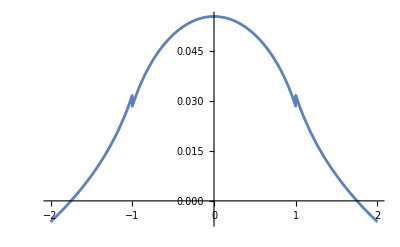

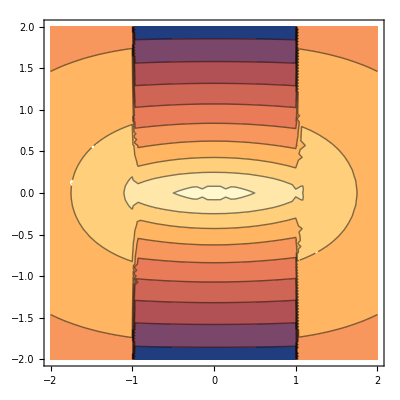

```mathematica
Plot[ReplaceAll[uxdefint2,{fx -> 1,fy ->0,μ->1,ν->0.25,yo->0}],{xo,-2,2}]
ContourPlot[ReplaceAll[uxdefint2,{fx -> 1,fy ->0,μ->1,ν->0.25}],{xo,-2,2},{yo,-2,2}]
```